Lab 10: Neutron Detectors

J.R. Powers-Luhn
NE550 Thursday 17:30

Utility tools

Raw SPE data

```mathematica
speraw[filename_,directory_]:=Import[directory<>filename]
```

SPE Data length

```mathematica
spedatalength[filename_,directory_]:=ToExpression[StringSplit[Import[directory<>filename][[12]]][[1,2]]]
```

```mathematica
spedatalength["He3 60s 0.5microseconds.Spe",NotebookDirectory[]<>"data/neutron detectors/"]
```

1023

SPE File Importer

```mathematica
spedata[filename_,directory_]:=ToExpression[Import[directory<>filename][[13;;13+spedatalength[filename,directory]]]][[;;,1]]
```

Time of count in SPE file

```mathematica
spetime[filename_,directory_]:=ToExpression[StringSplit[Import[directory<>filename][[10]]][[1,1]]]
```

^3 He neutron detector

1. Properly plot the ^3 He spectra for each shaping time investigated. Put all traces on a single pot, and use the full energy peak that shows up in at least some of the spectra to convert the abscissa to energy (Q-value is 764 keV).

```mathematica
shapingTimes={0.5,1,2,3,6,10}
filenameList=Table["He3 60s "<>ToString[i]<>"microseconds.Spe",{i,shapingTimes}]
```

{0.5,1,2,3,6,10}

{He3 60s 0.5microseconds.Spe,He3 60s 1microseconds.Spe,He3 60s 2microseconds.Spe,He3 60s 3microseconds.Spe,He3 60s 6microseconds.Spe,He3 60s 10microseconds.Spe}

```mathematica
directory=NotebookDirectory[]<>"data/neutron detectors/";
```

```mathematica
qvalue=764(*keV*);
```

```mathematica
peakindexes={68, 80, 88, 90, 94, 96}; (* From attached python script *)
xfrmfacts = qvalue / peakindexes //N
```

{11.2353,9.55,8.68182,8.48889,8.12766,7.95833}

```mathematica
xrange=Range[1,1023];
```

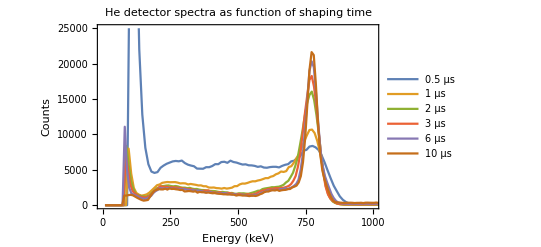

```mathematica
ListPlot[Table[Multicolumn[Join[xrange*xfrmfacts[[i]],spedata[filenameList[[i]],directory]],2]//First,{i,Length[filenameList]}],PlotRange->{{0,1000},{0,25000}},PlotLabel->Style["He detector spectra as function of shaping time",24,Black],ImageSize->Full,Joined->True,PlotLegends->Placed[Table[ToString[i]<>" μs",{i,shapingTimes}],{0.5,0.75}],Frame->True,FrameLabel->{Style["Energy (keV)",Black,20],Style["Counts",Black,20]},FrameTicksStyle->Directive[Black,16]]
```

2. From the plot, and in a text-style cell, discuss what shaping time is needed to obtain a quality spectrum from the ^3 He detector (i.e., full energy peak with wall effects).

In order to get a quality spectrum, a shaping time of 2μs is necessary, though for this source a longer shaping time is appropriate.

3. In another text-style cell, comment on the reason behind the required shaping time. That is, why is the peaking time found necessary required? What is it a function of?

The required shaping time is a function of how quickly the incident particle deposits its energy within the detector volume.

4. If we wish to only count neutron events, identify which energy value on the abscissa would be chosen to discriminate counts from the very low energy region of the spectrum. Put your answer in a text-style cell.

In order to only count neutron events, a threshold energy of ~160 keV is appropriate (for shaping time ≥1μs). This will cut the low energy background peaks while still including the wall effect region and the primary energy peak at the Q-value of 764 keV.

BF_3 neutron detector

1. Properly plot the BF_3 spectra for each shaping time investigated. Put all traces on a single plot, and use the full energy peak that shows up in at least some of the spectra to convert the abscissa to energy (Q-value is 2.79 MeV, but the ^7 Li product only goes to the ground state 6% of the time.

```mathematica
shapingTimes={0.5,1,2,3,6,10}
filenameList=Table["BF3 120s "<>ToString[i]<>"microseconds.Spe",{i,shapingTimes}]
```

{0.5,1,2,3,6,10}

{BF3 120s 0.5microseconds.Spe,BF3 120s 1microseconds.Spe,BF3 120s 2microseconds.Spe,BF3 120s 3microseconds.Spe,BF3 120s 6microseconds.Spe,BF3 120s 10microseconds.Spe}

```mathematica
directory=NotebookDirectory[]<>"data/neutron detectors/";
```

```mathematica
qvalue=2310(*keV; this is the excited^7 Li peak*);
```

```mathematica
peakindexes={133,150,164,167,174,181};

xfrmfacts = qvalue / peakindexes //N
```

{17.3684,15.4,14.0854,13.8323,13.2759,12.7624}

```mathematica
xrange=Range[1,1023];
```

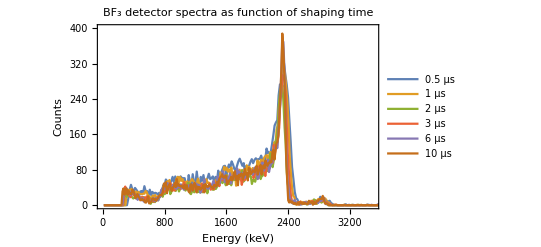

```mathematica
ListPlot[Table[Multicolumn[Join[xrange*xfrmfacts[[i]],spedata[filenameList[[i]],directory]],2]//First,{i,Length[filenameList]}],PlotRange->{{0,3500},{0,400}},PlotLabel->Style["BF_3 detector spectra as function of shaping time",24,Black],ImageSize->Full,Joined->True,PlotLegends->Placed[Table[ToString[i]<>" μs",{i,shapingTimes}],{0.5,0.75}],Frame->True,FrameLabel->{Style["Energy (keV)",Black,20],Style["Counts",Black,20]},FrameTicksStyle->Directive[Black,16]]
```

2. From the plot, and in a text-style cell, discuss what shaping time is needed to obtain a quality spectrum from the BF_3 detector (i.e., full energy peak with wall effects).

For this detector and source, a short shaping time of 0.5μs is appropriate. The ^7 Li and α are able to deposit most of their energy in this time range, meaning that spectroscopy is possible based on this relatively distinct peak.

The wall effect continuum appears from around 650 keV, with the second rise at around 1800keV.

3. In another text-style cell, comment on the reason behind the required shaping time. That is, why is the peaking time found necessary required? What is it a function of?

The required shaping time is based on the charge deposition rate in the detector. Once the shaping time expires, any energy that has yet to be deposited in the detector is discounted. Therefore a shaping time should be selected such that it collects as much of the energy from the radiation event as possible (or, in this case, the energy of the ^7 Li and the α), without collecting events from any subsequent event. It is a balance of source strength and incident particle energy/reaction Q-value.

4. If we wish to only count neutron events, identify which energy value on the abscissa would be chosen to discriminate counts from the very low energy region of the spectrum. Put your answer in a text-style cell.

To only count neutron events, we should set an energy threshold around 700 keV. This will include the wall effect continuum (where either the resultant alpha particle or ^7Li leaked out of the detector before depositing all of its energy). It will reject

Boron loaded organic scintillator

1. Plot the two spectra on the sample plot (properly formatted) when the Na-22 source is and is not present near the boron loaded organic scintillator.

2. Using the drawing tools, identify the thermal neutron response in both spectra (again, this is the plot in (1)) and the Na-22 contribution observed in one of the two spectra.

```mathematica
directory=NotebookDirectory[]<>"data/boron loaded organic scintillator/";
filenameList={"with Na.Spe","without Na.Spe"};
```

```mathematica
ListPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{All,{0,1000}},Joined->True,ImageSize->Full,PlotLegends->Placed[{"With Na","Without Na"},{0.85,0.85}],Frame->True,FrameLabel->{Style["Channel",Black,20],Style["Counts",Black,20]},PlotLabel->Style["Boron loaded organic scintillator and PuBe source\n with and without Na present",24,Black],FrameTicksStyle->Directive[Black,16]]
```

```mathematica
ListPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{{0,50},All},Joined->True,ImageSize->Full,PlotLegends->Placed[{"With Na","Without Na"},{0.85,0.85}],Frame->True,FrameLabel->{Style["Channel",Black,20],Style["Counts",Black,20]},PlotLabel->Style["Boron loaded organic scintillator and PuBe source\n with and without Na present",24,Black],FrameTicksStyle->Directive[Black,16]]
```

```mathematica
ListPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{{0,50},{0,20000}},Joined->True,ImageSize->Full,PlotLegends->Placed[{"With Na","Without Na"},{0.85,0.85}],Frame->True,FrameLabel->{Style["Channel",Black,20],Style["Counts",Black,20]},PlotLabel->Style["Boron loaded organic scintillator and PuBe source\n with and without Na present",24,Black],FrameTicksStyle->Directive[Black,16]]
```

3. In a text-style cell, comment on whether the Na-22 source interferes with counting thermal neutrons with this organic scintillator. Specifically comment on the threshold (i.e., value on the abscissa) you would choose to discriminate between gamma-rays and neutrons.

The Na-22 does not cause much interference with the neutron spectrum in this detector. As can be seen in the plot of channels 1-50, the two sources produce very similar curves, at least for this combination of settings and geometry. If the Na-22 contribution to this spectrum must be discounted entirely, however, using channels above the threshold value of 150 will give the neutron count only.

EJ-299 Pulse Shape Discrimination Plastic

1. Plot the two spectra on the sample plot (properly formatted) when the Na-22 source is and is not present near the EJ-299 detector.

2. Using the drawing tools, identify the fast neutron response in both spectra (again, this is the plot in (1)) and the Na-22 contribution observed in one of the two spectra.

```mathematica
directory=NotebookDirectory[]<>"data/EJ299/";
filenameList={"PuBe plus Na source EJ299.Spe","PuBe source EJ299.Spe"};
```

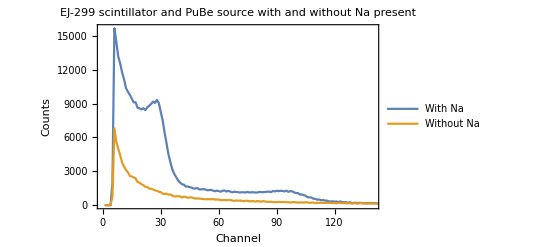

```mathematica
ListPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{{0,140},All},Joined->True,ImageSize->Full,PlotLegends->Placed[{"With Na","Without Na"},{0.85,0.85}],Frame->True,FrameLabel->{Style["Channel",Black,20],Style["Counts",Black,20]},PlotLabel->Style["EJ-299 scintillator and PuBe source\n with and without Na present",24,Black],FrameTicksStyle->Directive[Black,16]]
```

```mathematica
ListLogPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{All,All},Joined->True,ImageSize->Full,PlotLegends->Placed[{"With Na","Without Na"},{0.85,0.85}],Frame->True,FrameLabel->{Style["Channel",Black,20],Style["Counts",Black,20]},PlotLabel->Style["EJ-299 scintillator and PuBe source\n with and without Na present",24,Black],FrameTicksStyle->Directive[Black,16]]
```

3. In a text-style cell, comment on whether the Na-22 source interferes with counting fast neutrons with this organic scintillator. Specifically comment on the threshold (i.e., value on the abscissa) you would choose to discriminate between gamma-rays and neutrons, if any is appropriate at all.

The Na-22 source interferes with the counting of the fast neutrons. Due to the relative source strengths and detector efficiencies, the Na-22 swamps the PuBe neutrons, making them difficult to detect below the Q-value of the Na-22 decay (~1270 keV). Above this level there is good data to be gained on the spectrum for the partially thermalized but still fast neutrons.

4. Import the 2D PSD plot collected using the V1720 digitizer with PSD capability. Looking at this plot, qualitatively discuss, in a text-style cell, how well EJ-299 discriminates signals from gamma rays and neutrons. Pay particular attention to the lower integrated pulse region (low end of abscissa). For the abscissa value where a clear separation is observed between gamma rays and neutrons, theorize if this abscissa value is superior to just collecting a pulse height spectrum and choosing some threshold, if any (plot from (1) and discussion in (3)).

There is a clear separation of the neutron and gamma spectra at around ADC channel 2000. Without knowing more about the settings of the data collection chain it is difficult to determine quantitatively how much better this is than examining the spectra directly, but, assuming the two spectra represent the same energy ranges, the ADC channel of 2000/32768=0.061 compared to the non-PSD detection chain of 150/256=0.59 implies that the PSD method gives an order of magnitude improvement.